```mathematica
(*Function to compute and visualize dot products to find orthogonal vectors*)FindOrthogonalVectors[vectors_List,threshold_:1*^-3]:=Block[{n,dotProducts,orthogonalPairs,heatmap},
n=Length[vectors];
dotProducts=Table[Dot[vectors[[i]],vectors[[j]]],{i,n},{j,n}];
orthogonalPairs=Select[Flatten[Table[{i,j,dotProducts[[i,j]]},{i,n},{j,i,n}],1],Abs[#[[3]]]<threshold&];

heatmap=ArrayPlot[Abs[dotProducts],ColorFunction->"Rainbow",ColorFunctionScaling->True,PlotLabel->"Dot Product Heatmap",FrameTicks->{Automatic,Automatic},ImageSize->300,AspectRatio->1];

{orthogonalPairs,heatmap}
]
```

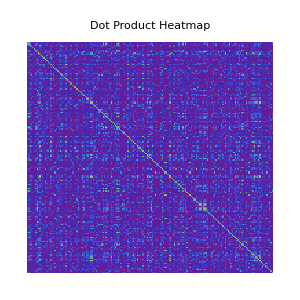

{{5,70,-0.613575},{11,62,-0.582124},{35,175,-0.394309},{61,167,0.0430341},{69,127,-0.310465},{120,134,-0.4979}}

```mathematica
(*Find orthogonal vectors with a threshold*)
data = allPersMeanOfDiff[[All,18]]
{orthogonalPairs,heatmap}=FindOrthogonalVectors[standardized,.7];

(*Display heatmap*)
heatmap
orthogonalPairs
```

```mathematica
MapAndSortOrthogonalPairs[orthogonalPairs_List,personalityNames_List]:=Module[{sortedPairs},
sortedPairs=SortBy[orthogonalPairs,Abs[#[[3]]]&];
Table[{personalityNames[[pair[[1]]]],personalityNames[[pair[[2]]]],pair[[3]]},{pair,sortedPairs}]]

mappedAndSortedPairs=MapAndSortOrthogonalPairs[orthogonalPairs,personalityNames];

mappedAndSortedPairs//TableForm
```

flexible | unpredictable | 0.0430341
greedy | practical thinker | -0.310465
creative | violent | -0.394309
perfectionist | resourceful | -0.4979
arrogant | flighty | -0.582124
ambitious | grounded | -0.613575